```mathematica
<<Radia`;
```

Radia Version: 4.31 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
magUp = radObjRecMag[{0,-100*^-6,100*^-6},{100*^-6,100*^-6,100*^-6},{0,1,0}];
magDown1 = radObjRecMag[{25*^-6,112.5*^-6,100*^-6},{50*^-6,25*^-6,100*^-6},{0,1,0}];
magDown2 = radObjRecMag[{12.5*^-6,137.5*^-6,100*^-6},{75*^-6,25*^-6,100*^-6},{0,1,0}];
magDown3 = radObjRecMag[{0,175*^-6,100*^-6},{100*^-6,50*^-6,100*^-6},{0,1,0}];
```

```mathematica
magnetContainer =radObjCnt[{magUp,magDown1,magDown2,magDown3}];
```

```mathematica
Show[Graphics3D[radObjDrw[magnetContainer]]]
```

-Graphics3D-

```mathematica
DensityPlot[radFld[magnetContainer,"bx",{x,y,-10*^-6}],{x,-100*^-6,100*^-6},{y,-100*^-6,100*^-6},PlotLegends->Automatic]
```

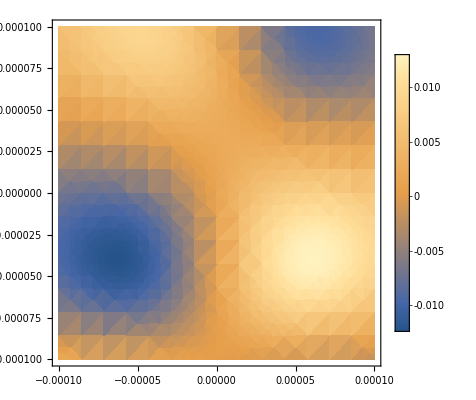
```mathematica
-Graphics-B_x
```

```mathematica
DensityPlot[radFld[magnetContainer,"by",{x,y,-10*^-6}],{x,-100*^-6,100*^-6},{y,-100*^-6,100*^-6},PlotLegends->Automatic]
```

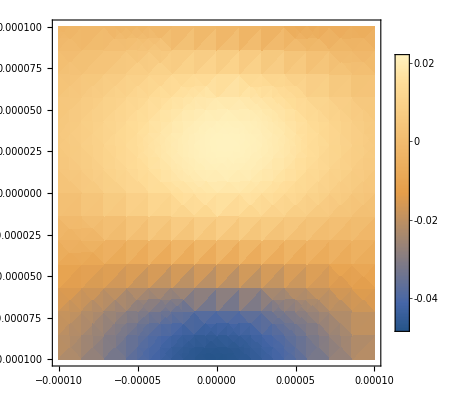
```mathematica
-Graphics-B_y
```

```mathematica
DensityPlot[radFld[magnetContainer,"bz",{x,y,-10*^-6}],{x,-100*^-6,100*^-6},{y,-100*^-6,100*^-6},PlotLegends->Automatic]
```

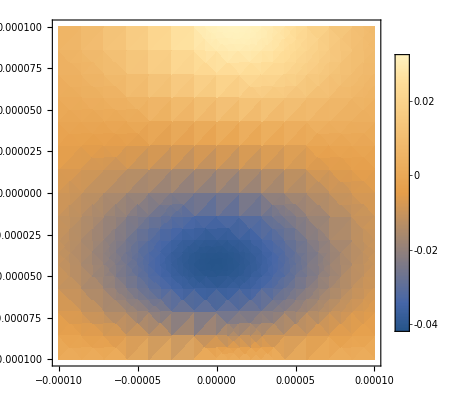
```mathematica
-Graphics-B_z
```